```mathematica
XY=Import["D:\\Uczelnia\FIZYKA\II ROK\I Semestr\Met_Num\Zestaw7\dane.dat"];
```

```mathematica
SplajnNat[XY0_] := Module[{XY=XY0}, 
Dd= Module[{k}, n = Length[XY]-1; X = Transpose[XY]_⟦1⟧; Y = Transpose[XY]_⟦2⟧; h=d = Table[0,{n}]; m = Table[0,{n+1}]; a=b=c=v = Table[0,{n-1}]; s = Table[0,{n},{4}]; 
h_⟦1⟧ = X_⟦2⟧ - X_⟦1⟧; 
d_⟦1⟧ = (Y_⟦2⟧ - Y_⟦1⟧)/h_⟦1⟧; 
For[ k=2, k≤n, k++, 
h_⟦k⟧ = X_⟦k+1⟧ - X_⟦k⟧; 
d_⟦k⟧ = (Y_⟦k+1⟧ - Y_⟦k⟧)/h_⟦k⟧; 
a_⟦k-1⟧ = h_⟦k⟧; 
b_⟦k-1⟧ = 2 (h_⟦k-1⟧ + h_⟦k⟧); 
c_⟦k-1⟧ = h_⟦k⟧; 
v_⟦k-1⟧ = 6 (d_⟦k⟧ - d_⟦k-1⟧)]; ]; 
TrD:=Module[{k,t}, 
m_⟦1⟧ = 0; 
m_⟦n+1⟧ = 0;
For[ k=2, k≤n-1, k++, 
t = a_⟦k-1⟧/b_⟦k-1⟧; 
b_⟦k⟧  =  b_⟦k⟧ - t  c_⟦k-1⟧; 
v_⟦k⟧  =  v_⟦k⟧ - t  v_⟦k-1⟧; ]; 
m_⟦n⟧  =  v_⟦n-1⟧/b_⟦n-1⟧; 
For[ k=n-2, 1≤k, k--, 
m_⟦k+1⟧ = (v_⟦k⟧ - c_⟦k⟧ m_⟦k+2⟧)/b_⟦k⟧; ]; ]; 
Pol:=Module[{k}, 
For[ k=1, k≤n, k++, 
s_⟦k,1⟧ = Y_⟦k⟧; 
s_⟦k,2⟧ = d_⟦k⟧ - 1/6 h_⟦k⟧ (2 m_⟦k⟧+m_⟦k+1⟧); 
s_⟦k,3⟧ = m_⟦k⟧/2; 
s_⟦k,4⟧ = (m_⟦k+1⟧ - m_⟦k⟧)/(6 h_⟦k⟧); ]; ]; 
CS[t_]:=Module[{j}, 
For[ j=1, j≤n, j++, 
If[ X_⟦j⟧≤t && t<X_⟦j+1⟧,k=j ]; ]; 
If[t<X_⟦1⟧,k=1 ]; 
If[X_⟦n+1⟧≤t,k=n ]; 
w = t - X_⟦k⟧; 
Return[ ((s_⟦k,4⟧ w+s_⟦k,3⟧) w+s_⟦k,2⟧) w+s_⟦k,1⟧ ]; ]; 

Dd; 
TrD; 
Pol; ]
```

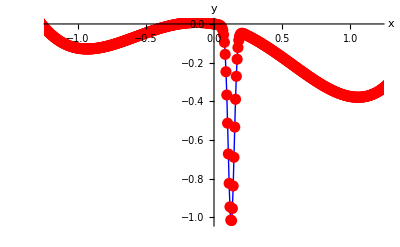

Splajn y = -0.538579+1.65361 x-2.70231 x^2+1.21179 x^3

```mathematica
SplajnNat[XY];   
dots=ListPlot[XY,PlotStyle->{Red,PointSize[0.02]},DisplayFunction->Identity];  
gr=Plot[CS[x],{x,-1.2,1.2},PlotStyle->{Blue},DisplayFunction->Identity];  
Show[gr,dots,AxesLabel->{"x","y    "}] 
Print["Splajn y = ",Expand[CS[x]]];
```